```mathematica
RandomFunction[WienerProcess[],{0,10,0.1},10]
```

TemporalData[…]

```mathematica
RandomFunction[WienerProcess[],{0,10,0.1}]
```

TemporalData[…]

```mathematica
Out[2]["Values"]
```

{0.,0.350729,0.606279,0.290364,0.250115,0.112097,0.591547,0.198949,-0.434811,-0.126691,0.296908,-0.537786,-0.714931,-1.01537,-0.730254,-1.11733,-1.1574,-1.16574,-1.27821,-0.772215,-0.353906,-0.512217,-0.621839,-0.585564,-0.708925,-0.859893,-0.778975,-0.771646,-0.371155,-0.163337,0.517142,0.317081,0.332175,0.880252,0.80519,0.764089,1.02472,1.44695,1.43938,1.22453,1.11998,1.2376,0.83628,0.728388,1.00303,1.24795,1.61263,1.45548,1.47713,2.15985,2.40164,2.72223,2.66939,2.67394,2.77376,2.80761,3.44459,3.09524,2.63276,2.59036,2.22987,1.97101,2.31703,3.08745,2.73796,1.92207,1.66332,1.52167,1.37307,1.51693,1.53867,1.68562,1.23527,0.964979,0.235745,-0.0944968,0.290856,0.157118,0.410878,0.219515,-0.390948,-0.138346,0.18463,0.288309,0.500435,0.344155,0.30813,0.596054,0.382245,0.0860911,0.250784,0.335228,0.249392,0.358895,0.519267,0.192255,0.0403907,-0.486568,-0.977161,-0.512971,-0.730727}

```mathematica
Out[2]["Properties"]
```

{Components,DateList,DatePath,DatePaths,Dates,FirstDates,FirstTimes,FirstValues,LastDates,LastTimes,LastValues,Part,Path,PathCount,PathFunction,PathFunctions,PathLength,PathLengths,Paths,PathTimes,SliceData,SliceDistribution,TimeList,Times,ValueDimensions,ValueList,Values}

```mathematica
Variance@{a,b,c}
```

1/6 ((2 a-b-c) Conjugate[a]+(-a+2 b-c) Conjugate[b]+(-a-b+2 c) Conjugate[c])

```mathematica
FullSimplify[Variance@{a,b,c},{a,b,c}∈Reals]
```

1/3 (a^2+b^2-b c+c^2-a (b+c))

```mathematica
FullSimplify[mean@{a,b,c},{a,b,c}∈Reals]
```

mean[{a,b,c}]

```mathematica
FullSimplify[Mean@{a,b,c},{a,b,c}∈Reals]
```

1/3 (a+b+c)

```mathematica
FullSimplify[Median@{a,b,c},{a,b,c}∈Reals]
```

Median[{a,b,c}]

```mathematica
Grid@
Map[{#,Out[2][#]}&,
Out[2]["Properties"]
]
```

Components | {TemporalData[…]}
DateList | {{Mon 1 Jan 1900 00:00:00GMT-8.,Mon 1 Jan 1900 00:00:00GMT-8.,Mon 1 Jan 1900 00:00:00GMT-8.,Mon 1 Jan 1900 00:00:00GMT-8.,Mon 1 Jan 1900 00:00:00GMT-8.,Mon 1 Jan 1900 00:00:00GMT-8.,Mon 1 Jan 1900 00:00:00GMT-8.,Mon 1 Jan 1900 00:00:00GMT-8.,Mon 1 Jan 1900 00:00:00GMT-8.,Mon 1 Jan 1900 00:00:00GMT-8.,Mon 1 Jan 1900 00:00:01GMT-8.,Mon 1 Jan 1900 00:00:01GMT-8.,Mon 1 Jan 1900 00:00:01GMT-8.,Mon 1 Jan 1900 00:00:01GMT-8.,Mon 1 Jan 1900 00:00:01GMT-8.,Mon 1 Jan 1900 00:00:01GMT-8.,Mon 1 Jan 1900 00:00:01GMT-8.,Mon 1 Jan 1900 00:00:01GMT-8.,Mon 1 Jan 1900 00:00:01GMT-8.,Mon 1 Jan 1900 00:00:01GMT-8.,Mon 1 Jan 1900 00:00:02GMT-8.,Mon 1 Jan 1900 00:00:02GMT-8.,Mon 1 Jan 1900 00:00:02GMT-8.,Mon 1 Jan 1900 00:00:02GMT-8.,Mon 1 Jan 1900 00:00:02GMT-8.,Mon 1 Jan 1900 00:00:02GMT-8.,Mon 1 Jan 1900 00:00:02GMT-8.,Mon 1 Jan 1900 00:00:02GMT-8.,Mon 1 Jan 1900 00:00:02GMT-8.,Mon 1 Jan 1900 00:00:02GMT-8.,Mon 1 Jan 1900 00:00:03GMT-8.,Mon 1 Jan 1900 00:00:03GMT-8.,Mon 1 Jan 1900 00:00:03GMT-8.,Mon 1 Jan 1900 00:00:03GMT-8.,Mon 1 Jan 1900 00:00:03GMT-8.,Mon 1 Jan 1900 00:00:03GMT-8.,Mon 1 Jan 1900 00:00:03GMT-8.,Mon 1 Jan 1900 00:00:03GMT-8.,Mon 1 Jan 1900 00:00:03GMT-8.,Mon 1 Jan 1900 00:00:03GMT-8.,Mon 1 Jan 1900 00:00:04GMT-8.,Mon 1 Jan 1900 00:00:04GMT-8.,Mon 1 Jan 1900 00:00:04GMT-8.,Mon 1 Jan 1900 00:00:04GMT-8.,Mon 1 Jan 1900 00:00:04GMT-8.,Mon 1 Jan 1900 00:00:04GMT-8.,Mon 1 Jan 1900 00:00:04GMT-8.,Mon 1 Jan 1900 00:00:04GMT-8.,Mon 1 Jan 1900 00:00:04GMT-8.,Mon 1 Jan 1900 00:00:04GMT-8.,Mon 1 Jan 1900 00:00:05GMT-8.,Mon 1 Jan 1900 00:00:05GMT-8.,Mon 1 Jan 1900 00:00:05GMT-8.,Mon 1 Jan 1900 00:00:05GMT-8.,Mon 1 Jan 1900 00:00:05GMT-8.,Mon 1 Jan 1900 00:00:05GMT-8.,Mon 1 Jan 1900 00:00:05GMT-8.,Mon 1 Jan 1900 00:00:05GMT-8.,Mon 1 Jan 1900 00:00:05GMT-8.,Mon 1 Jan 1900 00:00:05GMT-8.,Mon 1 Jan 1900 00:00:06GMT-8.,Mon 1 Jan 1900 00:00:06GMT-8.,Mon 1 Jan 1900 00:00:06GMT-8.,Mon 1 Jan 1900 00:00:06GMT-8.,Mon 1 Jan 1900 00:00:06GMT-8.,Mon 1 Jan 1900 00:00:06GMT-8.,Mon 1 Jan 1900 00:00:06GMT-8.,Mon 1 Jan 1900 00:00:06GMT-8.,Mon 1 Jan 1900 00:00:06GMT-8.,Mon 1 Jan 1900 00:00:06GMT-8.,Mon 1 Jan 1900 00:00:07GMT-8.,Mon 1 Jan 1900 00:00:07GMT-8.,Mon 1 Jan 1900 00:00:07GMT-8.,Mon 1 Jan 1900 00:00:07GMT-8.,Mon 1 Jan 1900 00:00:07GMT-8.,Mon 1 Jan 1900 00:00:07GMT-8.,Mon 1 Jan 1900 00:00:07GMT-8.,Mon 1 Jan 1900 00:00:07GMT-8.,Mon 1 Jan 1900 00:00:07GMT-8.,Mon 1 Jan 1900 00:00:07GMT-8.,Mon 1 Jan 1900 00:00:08GMT-8.,Mon 1 Jan 1900 00:00:08GMT-8.,Mon 1 Jan 1900 00:00:08GMT-8.,Mon 1 Jan 1900 00:00:08GMT-8.,Mon 1 Jan 1900 00:00:08GMT-8.,Mon 1 Jan 1900 00:00:08GMT-8.,Mon 1 Jan 1900 00:00:08GMT-8.,Mon 1 Jan 1900 00:00:08GMT-8.,Mon 1 Jan 1900 00:00:08GMT-8.,Mon 1 Jan 1900 00:00:08GMT-8.,Mon 1 Jan 1900 00:00:09GMT-8.,Mon 1 Jan 1900 00:00:09GMT-8.,Mon 1 Jan 1900 00:00:09GMT-8.,Mon 1 Jan 1900 00:00:09GMT-8.,Mon 1 Jan 1900 00:00:09GMT-8.,Mon 1 Jan 1900 00:00:09GMT-8.,Mon 1 Jan 1900 00:00:09GMT-8.,Mon 1 Jan 1900 00:00:09GMT-8.,Mon 1 Jan 1900 00:00:09GMT-8.,Mon 1 Jan 1900 00:00:09GMT-8.,Mon 1 Jan 1900 00:00:10GMT-8.}}
DatePath | {{Mon 1 Jan 1900 00:00:00GMT-8.,0.},{Mon 1 Jan 1900 00:00:00GMT-8.,0.350729},{Mon 1 Jan 1900 00:00:00GMT-8.,0.606279},{Mon 1 Jan 1900 00:00:00GMT-8.,0.290364},{Mon 1 Jan 1900 00:00:00GMT-8.,0.250115},{Mon 1 Jan 1900 00:00:00GMT-8.,0.112097},{Mon 1 Jan 1900 00:00:00GMT-8.,0.591547},{Mon 1 Jan 1900 00:00:00GMT-8.,0.198949},{Mon 1 Jan 1900 00:00:00GMT-8.,-0.434811},{Mon 1 Jan 1900 00:00:00GMT-8.,-0.126691},{Mon 1 Jan 1900 00:00:01GMT-8.,0.296908},{Mon 1 Jan 1900 00:00:01GMT-8.,-0.537786},{Mon 1 Jan 1900 00:00:01GMT-8.,-0.714931},{Mon 1 Jan 1900 00:00:01GMT-8.,-1.01537},{Mon 1 Jan 1900 00:00:01GMT-8.,-0.730254},{Mon 1 Jan 1900 00:00:01GMT-8.,-1.11733},{Mon 1 Jan 1900 00:00:01GMT-8.,-1.1574},{Mon 1 Jan 1900 00:00:01GMT-8.,-1.16574},{Mon 1 Jan 1900 00:00:01GMT-8.,-1.27821},{Mon 1 Jan 1900 00:00:01GMT-8.,-0.772215},{Mon 1 Jan 1900 00:00:02GMT-8.,-0.353906},{Mon 1 Jan 1900 00:00:02GMT-8.,-0.512217},{Mon 1 Jan 1900 00:00:02GMT-8.,-0.621839},{Mon 1 Jan 1900 00:00:02GMT-8.,-0.585564},{Mon 1 Jan 1900 00:00:02GMT-8.,-0.708925},{Mon 1 Jan 1900 00:00:02GMT-8.,-0.859893},{Mon 1 Jan 1900 00:00:02GMT-8.,-0.778975},{Mon 1 Jan 1900 00:00:02GMT-8.,-0.771646},{Mon 1 Jan 1900 00:00:02GMT-8.,-0.371155},{Mon 1 Jan 1900 00:00:02GMT-8.,-0.163337},{Mon 1 Jan 1900 00:00:03GMT-8.,0.517142},{Mon 1 Jan 1900 00:00:03GMT-8.,0.317081},{Mon 1 Jan 1900 00:00:03GMT-8.,0.332175},{Mon 1 Jan 1900 00:00:03GMT-8.,0.880252},{Mon 1 Jan 1900 00:00:03GMT-8.,0.80519},{Mon 1 Jan 1900 00:00:03GMT-8.,0.764089},{Mon 1 Jan 1900 00:00:03GMT-8.,1.02472},{Mon 1 Jan 1900 00:00:03GMT-8.,1.44695},{Mon 1 Jan 1900 00:00:03GMT-8.,1.43938},{Mon 1 Jan 1900 00:00:03GMT-8.,1.22453},{Mon 1 Jan 1900 00:00:04GMT-8.,1.11998},{Mon 1 Jan 1900 00:00:04GMT-8.,1.2376},{Mon 1 Jan 1900 00:00:04GMT-8.,0.83628},{Mon 1 Jan 1900 00:00:04GMT-8.,0.728388},{Mon 1 Jan 1900 00:00:04GMT-8.,1.00303},{Mon 1 Jan 1900 00:00:04GMT-8.,1.24795},{Mon 1 Jan 1900 00:00:04GMT-8.,1.61263},{Mon 1 Jan 1900 00:00:04GMT-8.,1.45548},{Mon 1 Jan 1900 00:00:04GMT-8.,1.47713},{Mon 1 Jan 1900 00:00:04GMT-8.,2.15985},{Mon 1 Jan 1900 00:00:05GMT-8.,2.40164},{Mon 1 Jan 1900 00:00:05GMT-8.,2.72223},{Mon 1 Jan 1900 00:00:05GMT-8.,2.66939},{Mon 1 Jan 1900 00:00:05GMT-8.,2.67394},{Mon 1 Jan 1900 00:00:05GMT-8.,2.77376},{Mon 1 Jan 1900 00:00:05GMT-8.,2.80761},{Mon 1 Jan 1900 00:00:05GMT-8.,3.44459},{Mon 1 Jan 1900 00:00:05GMT-8.,3.09524},{Mon 1 Jan 1900 00:00:05GMT-8.,2.63276},{Mon 1 Jan 1900 00:00:05GMT-8.,2.59036},{Mon 1 Jan 1900 00:00:06GMT-8.,2.22987},{Mon 1 Jan 1900 00:00:06GMT-8.,1.97101},{Mon 1 Jan 1900 00:00:06GMT-8.,2.31703},{Mon 1 Jan 1900 00:00:06GMT-8.,3.08745},{Mon 1 Jan 1900 00:00:06GMT-8.,2.73796},{Mon 1 Jan 1900 00:00:06GMT-8.,1.92207},{Mon 1 Jan 1900 00:00:06GMT-8.,1.66332},{Mon 1 Jan 1900 00:00:06GMT-8.,1.52167},{Mon 1 Jan 1900 00:00:06GMT-8.,1.37307},{Mon 1 Jan 1900 00:00:06GMT-8.,1.51693},{Mon 1 Jan 1900 00:00:07GMT-8.,1.53867},{Mon 1 Jan 1900 00:00:07GMT-8.,1.68562},{Mon 1 Jan 1900 00:00:07GMT-8.,1.23527},{Mon 1 Jan 1900 00:00:07GMT-8.,0.964979},{Mon 1 Jan 1900 00:00:07GMT-8.,0.235745},{Mon 1 Jan 1900 00:00:07GMT-8.,-0.0944968},{Mon 1 Jan 1900 00:00:07GMT-8.,0.290856},{Mon 1 Jan 1900 00:00:07GMT-8.,0.157118},{Mon 1 Jan 1900 00:00:07GMT-8.,0.410878},{Mon 1 Jan 1900 00:00:07GMT-8.,0.219515},{Mon 1 Jan 1900 00:00:08GMT-8.,-0.390948},{Mon 1 Jan 1900 00:00:08GMT-8.,-0.138346},{Mon 1 Jan 1900 00:00:08GMT-8.,0.18463},{Mon 1 Jan 1900 00:00:08GMT-8.,0.288309},{Mon 1 Jan 1900 00:00:08GMT-8.,0.500435},{Mon 1 Jan 1900 00:00:08GMT-8.,0.344155},{Mon 1 Jan 1900 00:00:08GMT-8.,0.30813},{Mon 1 Jan 1900 00:00:08GMT-8.,0.596054},{Mon 1 Jan 1900 00:00:08GMT-8.,0.382245},{Mon 1 Jan 1900 00:00:08GMT-8.,0.0860911},{Mon 1 Jan 1900 00:00:09GMT-8.,0.250784},{Mon 1 Jan 1900 00:00:09GMT-8.,0.335228},{Mon 1 Jan 1900 00:00:09GMT-8.,0.249392},{Mon 1 Jan 1900 00:00:09GMT-8.,0.358895},{Mon 1 Jan 1900 00:00:09GMT-8.,0.519267},{Mon 1 Jan 1900 00:00:09GMT-8.,0.192255},{Mon 1 Jan 1900 00:00:09GMT-8.,0.0403907},{Mon 1 Jan 1900 00:00:09GMT-8.,-0.486568},{Mon 1 Jan 1900 00:00:09GMT-8.,-0.977161},{Mon 1 Jan 1900 00:00:09GMT-8.,-0.512971},{Mon 1 Jan 1900 00:00:10GMT-8.,-0.730727}}
DatePaths | {{{Mon 1 Jan 1900 00:00:00GMT-8.,0.},{Mon 1 Jan 1900 00:00:00GMT-8.,0.350729},{Mon 1 Jan 1900 00:00:00GMT-8.,0.606279},{Mon 1 Jan 1900 00:00:00GMT-8.,0.290364},{Mon 1 Jan 1900 00:00:00GMT-8.,0.250115},{Mon 1 Jan 1900 00:00:00GMT-8.,0.112097},{Mon 1 Jan 1900 00:00:00GMT-8.,0.591547},{Mon 1 Jan 1900 00:00:00GMT-8.,0.198949},{Mon 1 Jan 1900 00:00:00GMT-8.,-0.434811},{Mon 1 Jan 1900 00:00:00GMT-8.,-0.126691},{Mon 1 Jan 1900 00:00:01GMT-8.,0.296908},{Mon 1 Jan 1900 00:00:01GMT-8.,-0.537786},{Mon 1 Jan 1900 00:00:01GMT-8.,-0.714931},{Mon 1 Jan 1900 00:00:01GMT-8.,-1.01537},{Mon 1 Jan 1900 00:00:01GMT-8.,-0.730254},{Mon 1 Jan 1900 00:00:01GMT-8.,-1.11733},{Mon 1 Jan 1900 00:00:01GMT-8.,-1.1574},{Mon 1 Jan 1900 00:00:01GMT-8.,-1.16574},{Mon 1 Jan 1900 00:00:01GMT-8.,-1.27821},{Mon 1 Jan 1900 00:00:01GMT-8.,-0.772215},{Mon 1 Jan 1900 00:00:02GMT-8.,-0.353906},{Mon 1 Jan 1900 00:00:02GMT-8.,-0.512217},{Mon 1 Jan 1900 00:00:02GMT-8.,-0.621839},{Mon 1 Jan 1900 00:00:02GMT-8.,-0.585564},{Mon 1 Jan 1900 00:00:02GMT-8.,-0.708925},{Mon 1 Jan 1900 00:00:02GMT-8.,-0.859893},{Mon 1 Jan 1900 00:00:02GMT-8.,-0.778975},{Mon 1 Jan 1900 00:00:02GMT-8.,-0.771646},{Mon 1 Jan 1900 00:00:02GMT-8.,-0.371155},{Mon 1 Jan 1900 00:00:02GMT-8.,-0.163337},{Mon 1 Jan 1900 00:00:03GMT-8.,0.517142},{Mon 1 Jan 1900 00:00:03GMT-8.,0.317081},{Mon 1 Jan 1900 00:00:03GMT-8.,0.332175},{Mon 1 Jan 1900 00:00:03GMT-8.,0.880252},{Mon 1 Jan 1900 00:00:03GMT-8.,0.80519},{Mon 1 Jan 1900 00:00:03GMT-8.,0.764089},{Mon 1 Jan 1900 00:00:03GMT-8.,1.02472},{Mon 1 Jan 1900 00:00:03GMT-8.,1.44695},{Mon 1 Jan 1900 00:00:03GMT-8.,1.43938},{Mon 1 Jan 1900 00:00:03GMT-8.,1.22453},{Mon 1 Jan 1900 00:00:04GMT-8.,1.11998},{Mon 1 Jan 1900 00:00:04GMT-8.,1.2376},{Mon 1 Jan 1900 00:00:04GMT-8.,0.83628},{Mon 1 Jan 1900 00:00:04GMT-8.,0.728388},{Mon 1 Jan 1900 00:00:04GMT-8.,1.00303},{Mon 1 Jan 1900 00:00:04GMT-8.,1.24795},{Mon 1 Jan 1900 00:00:04GMT-8.,1.61263},{Mon 1 Jan 1900 00:00:04GMT-8.,1.45548},{Mon 1 Jan 1900 00:00:04GMT-8.,1.47713},{Mon 1 Jan 1900 00:00:04GMT-8.,2.15985},{Mon 1 Jan 1900 00:00:05GMT-8.,2.40164},{Mon 1 Jan 1900 00:00:05GMT-8.,2.72223},{Mon 1 Jan 1900 00:00:05GMT-8.,2.66939},{Mon 1 Jan 1900 00:00:05GMT-8.,2.67394},{Mon 1 Jan 1900 00:00:05GMT-8.,2.77376},{Mon 1 Jan 1900 00:00:05GMT-8.,2.80761},{Mon 1 Jan 1900 00:00:05GMT-8.,3.44459},{Mon 1 Jan 1900 00:00:05GMT-8.,3.09524},{Mon 1 Jan 1900 00:00:05GMT-8.,2.63276},{Mon 1 Jan 1900 00:00:05GMT-8.,2.59036},{Mon 1 Jan 1900 00:00:06GMT-8.,2.22987},{Mon 1 Jan 1900 00:00:06GMT-8.,1.97101},{Mon 1 Jan 1900 00:00:06GMT-8.,2.31703},{Mon 1 Jan 1900 00:00:06GMT-8.,3.08745},{Mon 1 Jan 1900 00:00:06GMT-8.,2.73796},{Mon 1 Jan 1900 00:00:06GMT-8.,1.92207},{Mon 1 Jan 1900 00:00:06GMT-8.,1.66332},{Mon 1 Jan 1900 00:00:06GMT-8.,1.52167},{Mon 1 Jan 1900 00:00:06GMT-8.,1.37307},{Mon 1 Jan 1900 00:00:06GMT-8.,1.51693},{Mon 1 Jan 1900 00:00:07GMT-8.,1.53867},{Mon 1 Jan 1900 00:00:07GMT-8.,1.68562},{Mon 1 Jan 1900 00:00:07GMT-8.,1.23527},{Mon 1 Jan 1900 00:00:07GMT-8.,0.964979},{Mon 1 Jan 1900 00:00:07GMT-8.,0.235745},{Mon 1 Jan 1900 00:00:07GMT-8.,-0.0944968},{Mon 1 Jan 1900 00:00:07GMT-8.,0.290856},{Mon 1 Jan 1900 00:00:07GMT-8.,0.157118},{Mon 1 Jan 1900 00:00:07GMT-8.,0.410878},{Mon 1 Jan 1900 00:00:07GMT-8.,0.219515},{Mon 1 Jan 1900 00:00:08GMT-8.,-0.390948},{Mon 1 Jan 1900 00:00:08GMT-8.,-0.138346},{Mon 1 Jan 1900 00:00:08GMT-8.,0.18463},{Mon 1 Jan 1900 00:00:08GMT-8.,0.288309},{Mon 1 Jan 1900 00:00:08GMT-8.,0.500435},{Mon 1 Jan 1900 00:00:08GMT-8.,0.344155},{Mon 1 Jan 1900 00:00:08GMT-8.,0.30813},{Mon 1 Jan 1900 00:00:08GMT-8.,0.596054},{Mon 1 Jan 1900 00:00:08GMT-8.,0.382245},{Mon 1 Jan 1900 00:00:08GMT-8.,0.0860911},{Mon 1 Jan 1900 00:00:09GMT-8.,0.250784},{Mon 1 Jan 1900 00:00:09GMT-8.,0.335228},{Mon 1 Jan 1900 00:00:09GMT-8.,0.249392},{Mon 1 Jan 1900 00:00:09GMT-8.,0.358895},{Mon 1 Jan 1900 00:00:09GMT-8.,0.519267},{Mon 1 Jan 1900 00:00:09GMT-8.,0.192255},{Mon 1 Jan 1900 00:00:09GMT-8.,0.0403907},{Mon 1 Jan 1900 00:00:09GMT-8.,-0.486568},{Mon 1 Jan 1900 00:00:09GMT-8.,-0.977161},{Mon 1 Jan 1900 00:00:09GMT-8.,-0.512971},{Mon 1 Jan 1900 00:00:10GMT-8.,-0.730727}}}
Dates | {Mon 1 Jan 1900 00:00:00GMT-8.,Mon 1 Jan 1900 00:00:00GMT-8.,Mon 1 Jan 1900 00:00:00GMT-8.,Mon 1 Jan 1900 00:00:00GMT-8.,Mon 1 Jan 1900 00:00:00GMT-8.,Mon 1 Jan 1900 00:00:00GMT-8.,Mon 1 Jan 1900 00:00:00GMT-8.,Mon 1 Jan 1900 00:00:00GMT-8.,Mon 1 Jan 1900 00:00:00GMT-8.,Mon 1 Jan 1900 00:00:00GMT-8.,Mon 1 Jan 1900 00:00:01GMT-8.,Mon 1 Jan 1900 00:00:01GMT-8.,Mon 1 Jan 1900 00:00:01GMT-8.,Mon 1 Jan 1900 00:00:01GMT-8.,Mon 1 Jan 1900 00:00:01GMT-8.,Mon 1 Jan 1900 00:00:01GMT-8.,Mon 1 Jan 1900 00:00:01GMT-8.,Mon 1 Jan 1900 00:00:01GMT-8.,Mon 1 Jan 1900 00:00:01GMT-8.,Mon 1 Jan 1900 00:00:01GMT-8.,Mon 1 Jan 1900 00:00:02GMT-8.,Mon 1 Jan 1900 00:00:02GMT-8.,Mon 1 Jan 1900 00:00:02GMT-8.,Mon 1 Jan 1900 00:00:02GMT-8.,Mon 1 Jan 1900 00:00:02GMT-8.,Mon 1 Jan 1900 00:00:02GMT-8.,Mon 1 Jan 1900 00:00:02GMT-8.,Mon 1 Jan 1900 00:00:02GMT-8.,Mon 1 Jan 1900 00:00:02GMT-8.,Mon 1 Jan 1900 00:00:02GMT-8.,Mon 1 Jan 1900 00:00:03GMT-8.,Mon 1 Jan 1900 00:00:03GMT-8.,Mon 1 Jan 1900 00:00:03GMT-8.,Mon 1 Jan 1900 00:00:03GMT-8.,Mon 1 Jan 1900 00:00:03GMT-8.,Mon 1 Jan 1900 00:00:03GMT-8.,Mon 1 Jan 1900 00:00:03GMT-8.,Mon 1 Jan 1900 00:00:03GMT-8.,Mon 1 Jan 1900 00:00:03GMT-8.,Mon 1 Jan 1900 00:00:03GMT-8.,Mon 1 Jan 1900 00:00:04GMT-8.,Mon 1 Jan 1900 00:00:04GMT-8.,Mon 1 Jan 1900 00:00:04GMT-8.,Mon 1 Jan 1900 00:00:04GMT-8.,Mon 1 Jan 1900 00:00:04GMT-8.,Mon 1 Jan 1900 00:00:04GMT-8.,Mon 1 Jan 1900 00:00:04GMT-8.,Mon 1 Jan 1900 00:00:04GMT-8.,Mon 1 Jan 1900 00:00:04GMT-8.,Mon 1 Jan 1900 00:00:04GMT-8.,Mon 1 Jan 1900 00:00:05GMT-8.,Mon 1 Jan 1900 00:00:05GMT-8.,Mon 1 Jan 1900 00:00:05GMT-8.,Mon 1 Jan 1900 00:00:05GMT-8.,Mon 1 Jan 1900 00:00:05GMT-8.,Mon 1 Jan 1900 00:00:05GMT-8.,Mon 1 Jan 1900 00:00:05GMT-8.,Mon 1 Jan 1900 00:00:05GMT-8.,Mon 1 Jan 1900 00:00:05GMT-8.,Mon 1 Jan 1900 00:00:05GMT-8.,Mon 1 Jan 1900 00:00:06GMT-8.,Mon 1 Jan 1900 00:00:06GMT-8.,Mon 1 Jan 1900 00:00:06GMT-8.,Mon 1 Jan 1900 00:00:06GMT-8.,Mon 1 Jan 1900 00:00:06GMT-8.,Mon 1 Jan 1900 00:00:06GMT-8.,Mon 1 Jan 1900 00:00:06GMT-8.,Mon 1 Jan 1900 00:00:06GMT-8.,Mon 1 Jan 1900 00:00:06GMT-8.,Mon 1 Jan 1900 00:00:06GMT-8.,Mon 1 Jan 1900 00:00:07GMT-8.,Mon 1 Jan 1900 00:00:07GMT-8.,Mon 1 Jan 1900 00:00:07GMT-8.,Mon 1 Jan 1900 00:00:07GMT-8.,Mon 1 Jan 1900 00:00:07GMT-8.,Mon 1 Jan 1900 00:00:07GMT-8.,Mon 1 Jan 1900 00:00:07GMT-8.,Mon 1 Jan 1900 00:00:07GMT-8.,Mon 1 Jan 1900 00:00:07GMT-8.,Mon 1 Jan 1900 00:00:07GMT-8.,Mon 1 Jan 1900 00:00:08GMT-8.,Mon 1 Jan 1900 00:00:08GMT-8.,Mon 1 Jan 1900 00:00:08GMT-8.,Mon 1 Jan 1900 00:00:08GMT-8.,Mon 1 Jan 1900 00:00:08GMT-8.,Mon 1 Jan 1900 00:00:08GMT-8.,Mon 1 Jan 1900 00:00:08GMT-8.,Mon 1 Jan 1900 00:00:08GMT-8.,Mon 1 Jan 1900 00:00:08GMT-8.,Mon 1 Jan 1900 00:00:08GMT-8.,Mon 1 Jan 1900 00:00:09GMT-8.,Mon 1 Jan 1900 00:00:09GMT-8.,Mon 1 Jan 1900 00:00:09GMT-8.,Mon 1 Jan 1900 00:00:09GMT-8.,Mon 1 Jan 1900 00:00:09GMT-8.,Mon 1 Jan 1900 00:00:09GMT-8.,Mon 1 Jan 1900 00:00:09GMT-8.,Mon 1 Jan 1900 00:00:09GMT-8.,Mon 1 Jan 1900 00:00:09GMT-8.,Mon 1 Jan 1900 00:00:09GMT-8.,Mon 1 Jan 1900 00:00:10GMT-8.}
FirstDates | {Mon 1 Jan 1900 00:00:00GMT-8.}
FirstTimes | {0}
FirstValues | {0.}
LastDates | {Mon 1 Jan 1900 00:00:10GMT-8.}
LastTimes | {10}
LastValues | {-0.730727}
Part | TemporalData[…][Part]
Path | {{0.,0.},{0.1,0.350729},{0.2,0.606279},{0.3,0.290364},{0.4,0.250115},{0.5,0.112097},{0.6,0.591547},{0.7,0.198949},{0.8,-0.434811},{0.9,-0.126691},{1.,0.296908},{1.1,-0.537786},{1.2,-0.714931},{1.3,-1.01537},{1.4,-0.730254},{1.5,-1.11733},{1.6,-1.1574},{1.7,-1.16574},{1.8,-1.27821},{1.9,-0.772215},{2.,-0.353906},{2.1,-0.512217},{2.2,-0.621839},{2.3,-0.585564},{2.4,-0.708925},{2.5,-0.859893},{2.6,-0.778975},{2.7,-0.771646},{2.8,-0.371155},{2.9,-0.163337},{3.,0.517142},{3.1,0.317081},{3.2,0.332175},{3.3,0.880252},{3.4,0.80519},{3.5,0.764089},{3.6,1.02472},{3.7,1.44695},{3.8,1.43938},{3.9,1.22453},{4.,1.11998},{4.1,1.2376},{4.2,0.83628},{4.3,0.728388},{4.4,1.00303},{4.5,1.24795},{4.6,1.61263},{4.7,1.45548},{4.8,1.47713},{4.9,2.15985},{5.,2.40164},{5.1,2.72223},{5.2,2.66939},{5.3,2.67394},{5.4,2.77376},{5.5,2.80761},{5.6,3.44459},{5.7,3.09524},{5.8,2.63276},{5.9,2.59036},{6.,2.22987},{6.1,1.97101},{6.2,2.31703},{6.3,3.08745},{6.4,2.73796},{6.5,1.92207},{6.6,1.66332},{6.7,1.52167},{6.8,1.37307},{6.9,1.51693},{7.,1.53867},{7.1,1.68562},{7.2,1.23527},{7.3,0.964979},{7.4,0.235745},{7.5,-0.0944968},{7.6,0.290856},{7.7,0.157118},{7.8,0.410878},{7.9,0.219515},{8.,-0.390948},{8.1,-0.138346},{8.2,0.18463},{8.3,0.288309},{8.4,0.500435},{8.5,0.344155},{8.6,0.30813},{8.7,0.596054},{8.8,0.382245},{8.9,0.0860911},{9.,0.250784},{9.1,0.335228},{9.2,0.249392},{9.3,0.358895},{9.4,0.519267},{9.5,0.192255},{9.6,0.0403907},{9.7,-0.486568},{9.8,-0.977161},{9.9,-0.512971},{10.,-0.730727}}
PathCount | 1
PathFunction | Function[x,InterpolatingFunction[…][x],Listable]
PathFunctions | {Function[x,InterpolatingFunction[…][x],Listable]}
PathLength | 101
PathLengths | {101}
Paths | {{{0.,0.},{0.1,0.350729},{0.2,0.606279},{0.3,0.290364},{0.4,0.250115},{0.5,0.112097},{0.6,0.591547},{0.7,0.198949},{0.8,-0.434811},{0.9,-0.126691},{1.,0.296908},{1.1,-0.537786},{1.2,-0.714931},{1.3,-1.01537},{1.4,-0.730254},{1.5,-1.11733},{1.6,-1.1574},{1.7,-1.16574},{1.8,-1.27821},{1.9,-0.772215},{2.,-0.353906},{2.1,-0.512217},{2.2,-0.621839},{2.3,-0.585564},{2.4,-0.708925},{2.5,-0.859893},{2.6,-0.778975},{2.7,-0.771646},{2.8,-0.371155},{2.9,-0.163337},{3.,0.517142},{3.1,0.317081},{3.2,0.332175},{3.3,0.880252},{3.4,0.80519},{3.5,0.764089},{3.6,1.02472},{3.7,1.44695},{3.8,1.43938},{3.9,1.22453},{4.,1.11998},{4.1,1.2376},{4.2,0.83628},{4.3,0.728388},{4.4,1.00303},{4.5,1.24795},{4.6,1.61263},{4.7,1.45548},{4.8,1.47713},{4.9,2.15985},{5.,2.40164},{5.1,2.72223},{5.2,2.66939},{5.3,2.67394},{5.4,2.77376},{5.5,2.80761},{5.6,3.44459},{5.7,3.09524},{5.8,2.63276},{5.9,2.59036},{6.,2.22987},{6.1,1.97101},{6.2,2.31703},{6.3,3.08745},{6.4,2.73796},{6.5,1.92207},{6.6,1.66332},{6.7,1.52167},{6.8,1.37307},{6.9,1.51693},{7.,1.53867},{7.1,1.68562},{7.2,1.23527},{7.3,0.964979},{7.4,0.235745},{7.5,-0.0944968},{7.6,0.290856},{7.7,0.157118},{7.8,0.410878},{7.9,0.219515},{8.,-0.390948},{8.1,-0.138346},{8.2,0.18463},{8.3,0.288309},{8.4,0.500435},{8.5,0.344155},{8.6,0.30813},{8.7,0.596054},{8.8,0.382245},{8.9,0.0860911},{9.,0.250784},{9.1,0.335228},{9.2,0.249392},{9.3,0.358895},{9.4,0.519267},{9.5,0.192255},{9.6,0.0403907},{9.7,-0.486568},{9.8,-0.977161},{9.9,-0.512971},{10.,-0.730727}}}
PathTimes | {0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.}
SliceData | TemporalData[…][SliceData]
SliceDistribution | TemporalData[…][SliceDistribution]
TimeList | {{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.}}
Times | {0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.}
ValueDimensions | 1
ValueList | {{0.,0.350729,0.606279,0.290364,0.250115,0.112097,0.591547,0.198949,-0.434811,-0.126691,0.296908,-0.537786,-0.714931,-1.01537,-0.730254,-1.11733,-1.1574,-1.16574,-1.27821,-0.772215,-0.353906,-0.512217,-0.621839,-0.585564,-0.708925,-0.859893,-0.778975,-0.771646,-0.371155,-0.163337,0.517142,0.317081,0.332175,0.880252,0.80519,0.764089,1.02472,1.44695,1.43938,1.22453,1.11998,1.2376,0.83628,0.728388,1.00303,1.24795,1.61263,1.45548,1.47713,2.15985,2.40164,2.72223,2.66939,2.67394,2.77376,2.80761,3.44459,3.09524,2.63276,2.59036,2.22987,1.97101,2.31703,3.08745,2.73796,1.92207,1.66332,1.52167,1.37307,1.51693,1.53867,1.68562,1.23527,0.964979,0.235745,-0.0944968,0.290856,0.157118,0.410878,0.219515,-0.390948,-0.138346,0.18463,0.288309,0.500435,0.344155,0.30813,0.596054,0.382245,0.0860911,0.250784,0.335228,0.249392,0.358895,0.519267,0.192255,0.0403907,-0.486568,-0.977161,-0.512971,-0.730727}}
Values | {0.,0.350729,0.606279,0.290364,0.250115,0.112097,0.591547,0.198949,-0.434811,-0.126691,0.296908,-0.537786,-0.714931,-1.01537,-0.730254,-1.11733,-1.1574,-1.16574,-1.27821,-0.772215,-0.353906,-0.512217,-0.621839,-0.585564,-0.708925,-0.859893,-0.778975,-0.771646,-0.371155,-0.163337,0.517142,0.317081,0.332175,0.880252,0.80519,0.764089,1.02472,1.44695,1.43938,1.22453,1.11998,1.2376,0.83628,0.728388,1.00303,1.24795,1.61263,1.45548,1.47713,2.15985,2.40164,2.72223,2.66939,2.67394,2.77376,2.80761,3.44459,3.09524,2.63276,2.59036,2.22987,1.97101,2.31703,3.08745,2.73796,1.92207,1.66332,1.52167,1.37307,1.51693,1.53867,1.68562,1.23527,0.964979,0.235745,-0.0944968,0.290856,0.157118,0.410878,0.219515,-0.390948,-0.138346,0.18463,0.288309,0.500435,0.344155,0.30813,0.596054,0.382245,0.0860911,0.250784,0.335228,0.249392,0.358895,0.519267,0.192255,0.0403907,-0.486568,-0.977161,-0.512971,-0.730727}

```mathematica
Out[2]
```

TemporalData[…]

```mathematica
Out[2]["Path"]
```

{{0.,0.},{0.1,0.350729},{0.2,0.606279},{0.3,0.290364},{0.4,0.250115},{0.5,0.112097},{0.6,0.591547},{0.7,0.198949},{0.8,-0.434811},{0.9,-0.126691},{1.,0.296908},{1.1,-0.537786},{1.2,-0.714931},{1.3,-1.01537},{1.4,-0.730254},{1.5,-1.11733},{1.6,-1.1574},{1.7,-1.16574},{1.8,-1.27821},{1.9,-0.772215},{2.,-0.353906},{2.1,-0.512217},{2.2,-0.621839},{2.3,-0.585564},{2.4,-0.708925},{2.5,-0.859893},{2.6,-0.778975},{2.7,-0.771646},{2.8,-0.371155},{2.9,-0.163337},{3.,0.517142},{3.1,0.317081},{3.2,0.332175},{3.3,0.880252},{3.4,0.80519},{3.5,0.764089},{3.6,1.02472},{3.7,1.44695},{3.8,1.43938},{3.9,1.22453},{4.,1.11998},{4.1,1.2376},{4.2,0.83628},{4.3,0.728388},{4.4,1.00303},{4.5,1.24795},{4.6,1.61263},{4.7,1.45548},{4.8,1.47713},{4.9,2.15985},{5.,2.40164},{5.1,2.72223},{5.2,2.66939},{5.3,2.67394},{5.4,2.77376},{5.5,2.80761},{5.6,3.44459},{5.7,3.09524},{5.8,2.63276},{5.9,2.59036},{6.,2.22987},{6.1,1.97101},{6.2,2.31703},{6.3,3.08745},{6.4,2.73796},{6.5,1.92207},{6.6,1.66332},{6.7,1.52167},{6.8,1.37307},{6.9,1.51693},{7.,1.53867},{7.1,1.68562},{7.2,1.23527},{7.3,0.964979},{7.4,0.235745},{7.5,-0.0944968},{7.6,0.290856},{7.7,0.157118},{7.8,0.410878},{7.9,0.219515},{8.,-0.390948},{8.1,-0.138346},{8.2,0.18463},{8.3,0.288309},{8.4,0.500435},{8.5,0.344155},{8.6,0.30813},{8.7,0.596054},{8.8,0.382245},{8.9,0.0860911},{9.,0.250784},{9.1,0.335228},{9.2,0.249392},{9.3,0.358895},{9.4,0.519267},{9.5,0.192255},{9.6,0.0403907},{9.7,-0.486568},{9.8,-0.977161},{9.9,-0.512971},{10.,-0.730727}}

```mathematica
Out[2]["Values"]
```

{0.,0.350729,0.606279,0.290364,0.250115,0.112097,0.591547,0.198949,-0.434811,-0.126691,0.296908,-0.537786,-0.714931,-1.01537,-0.730254,-1.11733,-1.1574,-1.16574,-1.27821,-0.772215,-0.353906,-0.512217,-0.621839,-0.585564,-0.708925,-0.859893,-0.778975,-0.771646,-0.371155,-0.163337,0.517142,0.317081,0.332175,0.880252,0.80519,0.764089,1.02472,1.44695,1.43938,1.22453,1.11998,1.2376,0.83628,0.728388,1.00303,1.24795,1.61263,1.45548,1.47713,2.15985,2.40164,2.72223,2.66939,2.67394,2.77376,2.80761,3.44459,3.09524,2.63276,2.59036,2.22987,1.97101,2.31703,3.08745,2.73796,1.92207,1.66332,1.52167,1.37307,1.51693,1.53867,1.68562,1.23527,0.964979,0.235745,-0.0944968,0.290856,0.157118,0.410878,0.219515,-0.390948,-0.138346,0.18463,0.288309,0.500435,0.344155,0.30813,0.596054,0.382245,0.0860911,0.250784,0.335228,0.249392,0.358895,0.519267,0.192255,0.0403907,-0.486568,-0.977161,-0.512971,-0.730727}

```mathematica
Table[
{v,-Out[13][[v]]}
,{v,1,,10,.1}]
```

Table[{v,-%13⟦v⟧},{v,1,Null,10,0.1}]

```mathematica
Table[
{v,-Extract[Out[13],v]}
,{v,1,,10,.1}]
```

Table[{v,-Extract[%13,v]},{v,1,Null,10,0.1}]

```mathematica
Table[
{v,-Extract[Out[13],v]}
,{v,1,10,.1}]
```

{{1.,-Extract[{0.,0.350729,0.606279,0.290364,0.250115,0.112097,0.591547,87,0.519267,0.192255,0.0403907,-0.486568,-0.977161,-0.512971,-0.730727},1.]},89,{10.,-1}}
 |  |  |  |

```mathematica
Table[
v
,{v,1,10,.1}]
```

{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.}

```mathematica
Transpose[{Out[17],Out[13]}]
```

Transpose[{{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.},{0.,0.350729,0.606279,0.290364,0.250115,0.112097,0.591547,0.198949,-0.434811,-0.126691,0.296908,-0.537786,-0.714931,-1.01537,-0.730254,-1.11733,-1.1574,-1.16574,-1.27821,-0.772215,-0.353906,-0.512217,-0.621839,-0.585564,-0.708925,-0.859893,-0.778975,-0.771646,-0.371155,-0.163337,0.517142,0.317081,0.332175,0.880252,0.80519,0.764089,1.02472,1.44695,1.43938,1.22453,1.11998,1.2376,0.83628,0.728388,1.00303,1.24795,1.61263,1.45548,1.47713,2.15985,2.40164,2.72223,2.66939,2.67394,2.77376,2.80761,3.44459,3.09524,2.63276,2.59036,2.22987,1.97101,2.31703,3.08745,2.73796,1.92207,1.66332,1.52167,1.37307,1.51693,1.53867,1.68562,1.23527,0.964979,0.235745,-0.0944968,0.290856,0.157118,0.410878,0.219515,-0.390948,-0.138346,0.18463,0.288309,0.500435,0.344155,0.30813,0.596054,0.382245,0.0860911,0.250784,0.335228,0.249392,0.358895,0.519267,0.192255,0.0403907,-0.486568,-0.977161,-0.512971,-0.730727}}]

```mathematica
Table[
{Out[17][[i]],Out[13][[i]]},
{i,1,Length@Out[17],1}
]
```

{{1.,0.},{1.1,0.350729},{1.2,0.606279},{1.3,0.290364},{1.4,0.250115},{1.5,0.112097},{1.6,0.591547},{1.7,0.198949},{1.8,-0.434811},{1.9,-0.126691},{2.,0.296908},{2.1,-0.537786},{2.2,-0.714931},{2.3,-1.01537},{2.4,-0.730254},{2.5,-1.11733},{2.6,-1.1574},{2.7,-1.16574},{2.8,-1.27821},{2.9,-0.772215},{3.,-0.353906},{3.1,-0.512217},{3.2,-0.621839},{3.3,-0.585564},{3.4,-0.708925},{3.5,-0.859893},{3.6,-0.778975},{3.7,-0.771646},{3.8,-0.371155},{3.9,-0.163337},{4.,0.517142},{4.1,0.317081},{4.2,0.332175},{4.3,0.880252},{4.4,0.80519},{4.5,0.764089},{4.6,1.02472},{4.7,1.44695},{4.8,1.43938},{4.9,1.22453},{5.,1.11998},{5.1,1.2376},{5.2,0.83628},{5.3,0.728388},{5.4,1.00303},{5.5,1.24795},{5.6,1.61263},{5.7,1.45548},{5.8,1.47713},{5.9,2.15985},{6.,2.40164},{6.1,2.72223},{6.2,2.66939},{6.3,2.67394},{6.4,2.77376},{6.5,2.80761},{6.6,3.44459},{6.7,3.09524},{6.8,2.63276},{6.9,2.59036},{7.,2.22987},{7.1,1.97101},{7.2,2.31703},{7.3,3.08745},{7.4,2.73796},{7.5,1.92207},{7.6,1.66332},{7.7,1.52167},{7.8,1.37307},{7.9,1.51693},{8.,1.53867},{8.1,1.68562},{8.2,1.23527},{8.3,0.964979},{8.4,0.235745},{8.5,-0.0944968},{8.6,0.290856},{8.7,0.157118},{8.8,0.410878},{8.9,0.219515},{9.,-0.390948},{9.1,-0.138346},{9.2,0.18463},{9.3,0.288309},{9.4,0.500435},{9.5,0.344155},{9.6,0.30813},{9.7,0.596054},{9.8,0.382245},{9.9,0.0860911},{10.,0.250784}}

```mathematica
Table[
{Out[17][[i]],- Out[13][[i]]},
{i,1,Length@Out[17],1}
]
```

{{1.,0.},{1.1,-0.350729},{1.2,-0.606279},{1.3,-0.290364},{1.4,-0.250115},{1.5,-0.112097},{1.6,-0.591547},{1.7,-0.198949},{1.8,0.434811},{1.9,0.126691},{2.,-0.296908},{2.1,0.537786},{2.2,0.714931},{2.3,1.01537},{2.4,0.730254},{2.5,1.11733},{2.6,1.1574},{2.7,1.16574},{2.8,1.27821},{2.9,0.772215},{3.,0.353906},{3.1,0.512217},{3.2,0.621839},{3.3,0.585564},{3.4,0.708925},{3.5,0.859893},{3.6,0.778975},{3.7,0.771646},{3.8,0.371155},{3.9,0.163337},{4.,-0.517142},{4.1,-0.317081},{4.2,-0.332175},{4.3,-0.880252},{4.4,-0.80519},{4.5,-0.764089},{4.6,-1.02472},{4.7,-1.44695},{4.8,-1.43938},{4.9,-1.22453},{5.,-1.11998},{5.1,-1.2376},{5.2,-0.83628},{5.3,-0.728388},{5.4,-1.00303},{5.5,-1.24795},{5.6,-1.61263},{5.7,-1.45548},{5.8,-1.47713},{5.9,-2.15985},{6.,-2.40164},{6.1,-2.72223},{6.2,-2.66939},{6.3,-2.67394},{6.4,-2.77376},{6.5,-2.80761},{6.6,-3.44459},{6.7,-3.09524},{6.8,-2.63276},{6.9,-2.59036},{7.,-2.22987},{7.1,-1.97101},{7.2,-2.31703},{7.3,-3.08745},{7.4,-2.73796},{7.5,-1.92207},{7.6,-1.66332},{7.7,-1.52167},{7.8,-1.37307},{7.9,-1.51693},{8.,-1.53867},{8.1,-1.68562},{8.2,-1.23527},{8.3,-0.964979},{8.4,-0.235745},{8.5,0.0944968},{8.6,-0.290856},{8.7,-0.157118},{8.8,-0.410878},{8.9,-0.219515},{9.,0.390948},{9.1,0.138346},{9.2,-0.18463},{9.3,-0.288309},{9.4,-0.500435},{9.5,-0.344155},{9.6,-0.30813},{9.7,-0.596054},{9.8,-0.382245},{9.9,-0.0860911},{10.,-0.250784}}

```mathematica
TemporalData[Out[13],{Out[17]}]
```

TemporalData[{0.,0.350729,0.606279,0.290364,0.250115,0.112097,0.591547,0.198949,-0.434811,-0.126691,0.296908,-0.537786,-0.714931,-1.01537,-0.730254,-1.11733,-1.1574,-1.16574,-1.27821,-0.772215,-0.353906,-0.512217,-0.621839,-0.585564,-0.708925,-0.859893,-0.778975,-0.771646,-0.371155,-0.163337,0.517142,0.317081,0.332175,0.880252,0.80519,0.764089,1.02472,1.44695,1.43938,1.22453,1.11998,1.2376,0.83628,0.728388,1.00303,1.24795,1.61263,1.45548,1.47713,2.15985,2.40164,2.72223,2.66939,2.67394,2.77376,2.80761,3.44459,3.09524,2.63276,2.59036,2.22987,1.97101,2.31703,3.08745,2.73796,1.92207,1.66332,1.52167,1.37307,1.51693,1.53867,1.68562,1.23527,0.964979,0.235745,-0.0944968,0.290856,0.157118,0.410878,0.219515,-0.390948,-0.138346,0.18463,0.288309,0.500435,0.344155,0.30813,0.596054,0.382245,0.0860911,0.250784,0.335228,0.249392,0.358895,0.519267,0.192255,0.0403907,-0.486568,-0.977161,-0.512971,-0.730727},{{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.}}]

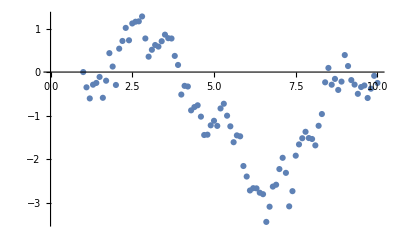

```mathematica
ListPlot@Out[20]
```

```mathematica
ListPlot[Out[20],Out[2]]
```

ListPlot[{{1.,0.},{1.1,-0.350729},{1.2,-0.606279},{1.3,-0.290364},{1.4,-0.250115},{1.5,-0.112097},{1.6,-0.591547},{1.7,-0.198949},{1.8,0.434811},{1.9,0.126691},{2.,-0.296908},{2.1,0.537786},{2.2,0.714931},{2.3,1.01537},{2.4,0.730254},{2.5,1.11733},{2.6,1.1574},{2.7,1.16574},{2.8,1.27821},{2.9,0.772215},{3.,0.353906},{3.1,0.512217},{3.2,0.621839},{3.3,0.585564},{3.4,0.708925},{3.5,0.859893},{3.6,0.778975},{3.7,0.771646},{3.8,0.371155},{3.9,0.163337},{4.,-0.517142},{4.1,-0.317081},{4.2,-0.332175},{4.3,-0.880252},{4.4,-0.80519},{4.5,-0.764089},{4.6,-1.02472},{4.7,-1.44695},{4.8,-1.43938},{4.9,-1.22453},{5.,-1.11998},{5.1,-1.2376},{5.2,-0.83628},{5.3,-0.728388},{5.4,-1.00303},{5.5,-1.24795},{5.6,-1.61263},{5.7,-1.45548},{5.8,-1.47713},{5.9,-2.15985},{6.,-2.40164},{6.1,-2.72223},{6.2,-2.66939},{6.3,-2.67394},{6.4,-2.77376},{6.5,-2.80761},{6.6,-3.44459},{6.7,-3.09524},{6.8,-2.63276},{6.9,-2.59036},{7.,-2.22987},{7.1,-1.97101},{7.2,-2.31703},{7.3,-3.08745},{7.4,-2.73796},{7.5,-1.92207},{7.6,-1.66332},{7.7,-1.52167},{7.8,-1.37307},{7.9,-1.51693},{8.,-1.53867},{8.1,-1.68562},{8.2,-1.23527},{8.3,-0.964979},{8.4,-0.235745},{8.5,0.0944968},{8.6,-0.290856},{8.7,-0.157118},{8.8,-0.410878},{8.9,-0.219515},{9.,0.390948},{9.1,0.138346},{9.2,-0.18463},{9.3,-0.288309},{9.4,-0.500435},{9.5,-0.344155},{9.6,-0.30813},{9.7,-0.596054},{9.8,-0.382245},{9.9,-0.0860911},{10.,-0.250784}},TemporalData[…]]

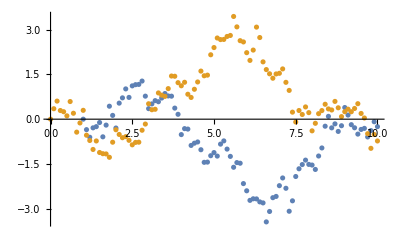

```mathematica
ListPlot[{Out[20],Out[2]}]
```

```mathematica
Correlation[Map[Last,Out[20]],Out[2]["Values"]]
```

Correlation[{0.,-0.350729,-0.606279,-0.290364,-0.250115,-0.112097,-0.591547,-0.198949,0.434811,0.126691,-0.296908,0.537786,0.714931,1.01537,0.730254,1.11733,1.1574,1.16574,1.27821,0.772215,0.353906,0.512217,0.621839,0.585564,0.708925,0.859893,0.778975,0.771646,0.371155,0.163337,-0.517142,-0.317081,-0.332175,-0.880252,-0.80519,-0.764089,-1.02472,-1.44695,-1.43938,-1.22453,-1.11998,-1.2376,-0.83628,-0.728388,-1.00303,-1.24795,-1.61263,-1.45548,-1.47713,-2.15985,-2.40164,-2.72223,-2.66939,-2.67394,-2.77376,-2.80761,-3.44459,-3.09524,-2.63276,-2.59036,-2.22987,-1.97101,-2.31703,-3.08745,-2.73796,-1.92207,-1.66332,-1.52167,-1.37307,-1.51693,-1.53867,-1.68562,-1.23527,-0.964979,-0.235745,0.0944968,-0.290856,-0.157118,-0.410878,-0.219515,0.390948,0.138346,-0.18463,-0.288309,-0.500435,-0.344155,-0.30813,-0.596054,-0.382245,-0.0860911,-0.250784},{0.,0.350729,0.606279,0.290364,0.250115,0.112097,0.591547,0.198949,-0.434811,-0.126691,0.296908,-0.537786,-0.714931,-1.01537,-0.730254,-1.11733,-1.1574,-1.16574,-1.27821,-0.772215,-0.353906,-0.512217,-0.621839,-0.585564,-0.708925,-0.859893,-0.778975,-0.771646,-0.371155,-0.163337,0.517142,0.317081,0.332175,0.880252,0.80519,0.764089,1.02472,1.44695,1.43938,1.22453,1.11998,1.2376,0.83628,0.728388,1.00303,1.24795,1.61263,1.45548,1.47713,2.15985,2.40164,2.72223,2.66939,2.67394,2.77376,2.80761,3.44459,3.09524,2.63276,2.59036,2.22987,1.97101,2.31703,3.08745,2.73796,1.92207,1.66332,1.52167,1.37307,1.51693,1.53867,1.68562,1.23527,0.964979,0.235745,-0.0944968,0.290856,0.157118,0.410878,0.219515,-0.390948,-0.138346,0.18463,0.288309,0.500435,0.344155,0.30813,0.596054,0.382245,0.0860911,0.250784,0.335228,0.249392,0.358895,0.519267,0.192255,0.0403907,-0.486568,-0.977161,-0.512971,-0.730727}]

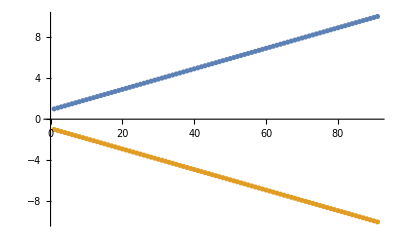

```mathematica
ListPlot[{Out[17],-Out[17]}]
```

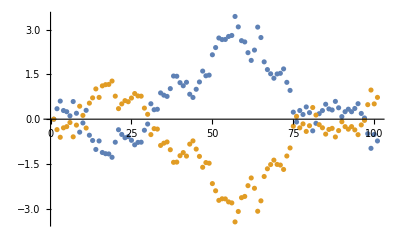

```mathematica
ListPlot[{Out[13],-Out[13]}]
```

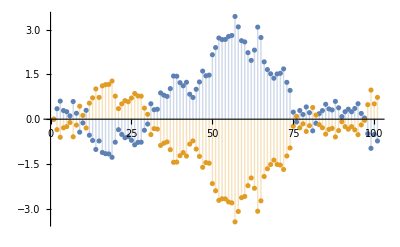

```mathematica
ListPlot[{Out[13],-Out[13]},Filling->Axis]
```

```mathematica
ListPlot[{Out[13],-Out[13]},Filling->Axis,PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
ListPlot[{Out[13],-Out[13]},Filling->Axis]
```

```mathematica
Correlation[Out[13],-Out[13]]
```

-1.

```mathematica
Min@Out@13
```

-1.27821

```mathematica
1+Min@Out@13+Out[13]
```

{-0.278206,0.0725225,0.328073,0.0121579,-0.0280915,-0.166109,0.313341,-0.0792572,-0.713017,-0.404897,0.0187018,-0.815992,-0.993137,-1.29358,-1.00846,-1.39553,-1.43561,-1.44395,-1.55641,-1.05042,-0.632112,-0.790423,-0.900045,-0.86377,-0.987131,-1.1381,-1.05718,-1.04985,-0.649361,-0.441543,0.238936,0.0388748,0.0539689,0.602046,0.526984,0.485883,0.746513,1.16874,1.16117,0.946329,0.841775,0.959399,0.558074,0.450182,0.724828,0.969744,1.33442,1.17727,1.19892,1.88165,2.12343,2.44402,2.39119,2.39573,2.49555,2.52941,3.16638,2.81703,2.35455,2.31216,1.95166,1.6928,2.03882,2.80925,2.45975,1.64386,1.38511,1.24347,1.09487,1.23872,1.26046,1.40741,0.957062,0.686772,-0.0424615,-0.372703,0.0126502,-0.121089,0.132672,-0.0586908,-0.669154,-0.416552,-0.0935758,0.0101029,0.222229,0.0659485,0.0299243,0.317847,0.104039,-0.192115,-0.0274217,0.057022,-0.0288143,0.0806885,0.241061,-0.0859515,-0.237815,-0.764774,-1.25537,-0.791177,-1.00893}

```mathematica
2+Out[13]
```

{2.,2.35073,2.60628,2.29036,2.25011,2.1121,2.59155,2.19895,1.56519,1.87331,2.29691,1.46221,1.28507,0.984631,1.26975,0.882672,0.8426,0.834258,0.721794,1.22779,1.64609,1.48778,1.37816,1.41444,1.29108,1.14011,1.22103,1.22835,1.62885,1.83666,2.51714,2.31708,2.33217,2.88025,2.80519,2.76409,3.02472,3.44695,3.43938,3.22453,3.11998,3.2376,2.83628,2.72839,3.00303,3.24795,3.61263,3.45548,3.47713,4.15985,4.40164,4.72223,4.66939,4.67394,4.77376,4.80761,5.44459,5.09524,4.63276,4.59036,4.22987,3.97101,4.31703,5.08745,4.73796,3.92207,3.66332,3.52167,3.37307,3.51693,3.53867,3.68562,3.23527,2.96498,2.23574,1.9055,2.29086,2.15712,2.41088,2.21952,1.60905,1.86165,2.18463,2.28831,2.50043,2.34415,2.30813,2.59605,2.38225,2.08609,2.25078,2.33523,2.24939,2.35889,2.51927,2.19225,2.04039,1.51343,1.02284,1.48703,1.26927}

```mathematica
Correlation[Out[33],-Out[33]]
```

-1.

```mathematica
Variance@Out@33
```

1.32467

```mathematica
Mean@Out@33
```

2.65093

```mathematica
Median@Out@33
```

2.35073

```mathematica
Min@Out@33
```

0.721794

```mathematica
Max@Out@33
```

5.44459

```mathematica
100(Max[Out[33]]-Min[Out[33]])
```

472.279

```mathematica
Max[Out[33]]/Min[Out[33]]
```

7.54313

```mathematica
100Max[Out[33]]
```

544.459

```mathematica
100Min[Out[33]]
```

72.1794

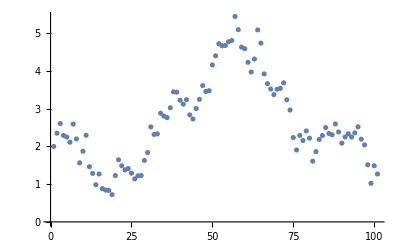

```mathematica
ListPlot@Out[33]
```

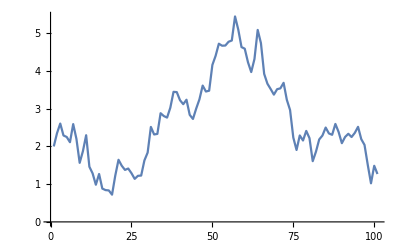

```mathematica
ListLinePlot@Out[33]
```

```mathematica
Sign[Out[33]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Sign[Differences@Out[33]]
```

{1,1,-1,-1,-1,1,-1,-1,1,1,-1,-1,-1,1,-1,-1,-1,-1,1,1,-1,-1,1,-1,-1,1,1,1,1,1,-1,1,1,-1,-1,1,1,-1,-1,-1,1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,1,1,-1,-1,-1,-1,-1,1,1,-1,-1,-1,-1,-1,1,1,1,-1,-1,-1,-1,1,-1,1,-1,-1,1,1,1,1,-1,-1,1,-1,-1,1,1,-1,1,1,-1,-1,-1,-1,1,-1}

```mathematica
100Extract[Out[33],1]
```

200.

```mathematica
Extract[Out[33],1]
```

2.

```mathematica
Extract[Out[33],2]
```

2.35073

```mathematica
Extract[Out[33],2]
```

```mathematica
Partition[Out[47],2,1]
```

{{1,1},{1,-1},{-1,-1},{-1,-1},{-1,1},{1,-1},{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1},{-1,-1},{-1,1},{1,-1},{-1,-1},{-1,-1},{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1},{-1,1},{1,-1},{-1,-1},{-1,1},{1,1},{1,1},{1,1},{1,1},{1,-1},{-1,1},{1,1},{1,-1},{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1},{-1,-1},{-1,1},{1,-1},{-1,-1},{-1,1},{1,1},{1,1},{1,-1},{-1,1},{1,1},{1,1},{1,1},{1,-1},{-1,1},{1,1},{1,1},{1,1},{1,-1},{-1,-1},{-1,-1},{-1,-1},{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1},{-1,-1},{-1,-1},{-1,-1},{-1,1},{1,1},{1,1},{1,-1},{-1,-1},{-1,-1},{-1,-1},{-1,1},{1,-1},{-1,1},{1,-1},{-1,-1},{-1,1},{1,1},{1,1},{1,1},{1,-1},{-1,-1},{-1,1},{1,-1},{-1,-1},{-1,1},{1,1},{1,-1},{-1,1},{1,1},{1,-1},{-1,-1},{-1,-1},{-1,-1},{-1,1},{1,-1}}

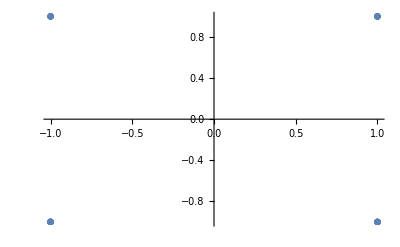

```mathematica
ListPlot[Out[51]]
```

```mathematica
Histogram3D[Out[51]]
```

-Graphics3D-

```mathematica
Partition[Differences@Out[33],2,1]
```

{{0.350729,0.255551},{0.255551,-0.315916},{-0.315916,-0.0402494},{-0.0402494,-0.138017},{-0.138017,0.47945},{0.47945,-0.392598},{-0.392598,-0.63376},{-0.63376,0.30812},{0.30812,0.423599},{0.423599,-0.834694},{-0.834694,-0.177145},{-0.177145,-0.300439},{-0.300439,0.285115},{0.285115,-0.387074},{-0.387074,-0.0400715},{-0.0400715,-0.00834244},{-0.00834244,-0.112464},{-0.112464,0.505991},{0.505991,0.418309},{0.418309,-0.158311},{-0.158311,-0.109622},{-0.109622,0.0362748},{0.0362748,-0.123361},{-0.123361,-0.150968},{-0.150968,0.0809177},{0.0809177,0.00732875},{0.00732875,0.400491},{0.400491,0.207818},{0.207818,0.680478},{0.680478,-0.200061},{-0.200061,0.0150941},{0.0150941,0.548077},{0.548077,-0.0750615},{-0.0750615,-0.0411011},{-0.0411011,0.26063},{0.26063,0.422231},{0.422231,-0.00757164},{-0.00757164,-0.214844},{-0.214844,-0.104554},{-0.104554,0.117624},{0.117624,-0.401325},{-0.401325,-0.107891},{-0.107891,0.274645},{0.274645,0.244916},{0.244916,0.364681},{0.364681,-0.15715},{-0.15715,0.0216477},{0.0216477,0.682723},{0.682723,0.241787},{0.241787,0.320591},{0.320591,-0.0528368},{-0.0528368,0.00454378},{0.00454378,0.0998182},{0.0998182,0.0338591},{0.0338591,0.636971},{0.636971,-0.349349},{-0.349349,-0.462477},{-0.462477,-0.0423957},{-0.0423957,-0.360494},{-0.360494,-0.258863},{-0.258863,0.34602},{0.34602,0.770427},{0.770427,-0.349495},{-0.349495,-0.815892},{-0.815892,-0.258747},{-0.258747,-0.141647},{-0.141647,-0.148601},{-0.148601,0.143858},{0.143858,0.0217362},{0.0217362,0.146949},{0.146949,-0.450347},{-0.450347,-0.270289},{-0.270289,-0.729234},{-0.729234,-0.330241},{-0.330241,0.385353},{0.385353,-0.133739},{-0.133739,0.25376},{0.25376,-0.191362},{-0.191362,-0.610463},{-0.610463,0.252602},{0.252602,0.322976},{0.322976,0.103679},{0.103679,0.212126},{0.212126,-0.15628},{-0.15628,-0.0360242},{-0.0360242,0.287923},{0.287923,-0.213808},{-0.213808,-0.296154},{-0.296154,0.164693},{0.164693,0.0844437},{0.0844437,-0.0858362},{-0.0858362,0.109503},{0.109503,0.160372},{0.160372,-0.327012},{-0.327012,-0.151864},{-0.151864,-0.526959},{-0.526959,-0.490592},{-0.490592,0.46419},{0.46419,-0.217757}}

```mathematica
Histogram3D@Partition[Differences@Out[33],2,1]
```

-Graphics3D-

```mathematica
Partition[Ratios@Out[33],2,1]
```

{{1.17536,1.10871},{1.10871,0.878787},{0.878787,0.982427},{0.982427,0.938662},{0.938662,1.227},{1.227,0.848508},{0.848508,0.71179},{0.71179,1.19686},{1.19686,1.22612},{1.22612,0.636601},{0.636601,0.878852},{0.878852,0.766208},{0.766208,1.28957},{1.28957,0.695156},{0.695156,0.954602},{0.954602,0.990099},{0.990099,0.865193},{0.865193,1.70102},{1.70102,1.3407},{1.3407,0.903826},{0.903826,0.926319},{0.926319,1.02632},{1.02632,0.912785},{0.912785,0.883068},{0.883068,1.07097},{1.07097,1.006},{1.006,1.32604},{1.32604,1.12759},{1.12759,1.3705},{1.3705,0.920521},{0.920521,1.00651},{1.00651,1.23501},{1.23501,0.973939},{0.973939,0.985348},{0.985348,1.09429},{1.09429,1.13959},{1.13959,0.997803},{0.997803,0.937534},{0.937534,0.967576},{0.967576,1.0377},{1.0377,0.876043},{0.876043,0.96196},{0.96196,1.10066},{1.10066,1.08156},{1.08156,1.11228},{1.11228,0.9565},{0.9565,1.00626},{1.00626,1.19635},{1.19635,1.05812},{1.05812,1.07283},{1.07283,0.988811},{0.988811,1.00097},{1.00097,1.02136},{1.02136,1.00709},{1.00709,1.13249},{1.13249,0.935835},{0.935835,0.909234},{0.909234,0.990849},{0.990849,0.921467},{0.921467,0.938801},{0.938801,1.08714},{1.08714,1.17846},{1.17846,0.931303},{0.931303,0.827797},{0.827797,0.934028},{0.934028,0.961334},{0.961334,0.957804},{0.957804,1.04265},{1.04265,1.00618},{1.00618,1.04153},{1.04153,0.877809},{0.877809,0.916455},{0.916455,0.754051},{0.754051,0.85229},{0.85229,1.20223},{1.20223,0.941621},{0.941621,1.11764},{1.11764,0.920625},{0.920625,0.724956},{0.724956,1.15699},{1.15699,1.17349},{1.17349,1.04746},{1.04746,1.0927},{1.0927,0.937499},{0.937499,0.984632},{0.984632,1.12474},{1.12474,0.917641},{0.917641,0.875683},{0.875683,1.07895},{1.07895,1.03752},{1.03752,0.963243},{0.963243,1.04868},{1.04868,1.06799},{1.06799,0.870195},{0.870195,0.930727},{0.930727,0.741736},{0.741736,0.675841},{0.675841,1.45382},{1.45382,0.853563}}

```mathematica
Histogram3D[Out[56]]
```

-Graphics3D-

```mathematica
(Min@Out[33])/Max[Out[33]]
```

0.132571

```mathematica
((Min@Out[33])/Max[Out[33]])^-1
```

7.54313

```mathematica
PercentForm[Out[59]]
```

754.3%

```mathematica
Out[33]
```

{2.,2.35073,2.60628,2.29036,2.25011,2.1121,2.59155,2.19895,1.56519,1.87331,2.29691,1.46221,1.28507,0.984631,1.26975,0.882672,0.8426,0.834258,0.721794,1.22779,1.64609,1.48778,1.37816,1.41444,1.29108,1.14011,1.22103,1.22835,1.62885,1.83666,2.51714,2.31708,2.33217,2.88025,2.80519,2.76409,3.02472,3.44695,3.43938,3.22453,3.11998,3.2376,2.83628,2.72839,3.00303,3.24795,3.61263,3.45548,3.47713,4.15985,4.40164,4.72223,4.66939,4.67394,4.77376,4.80761,5.44459,5.09524,4.63276,4.59036,4.22987,3.97101,4.31703,5.08745,4.73796,3.92207,3.66332,3.52167,3.37307,3.51693,3.53867,3.68562,3.23527,2.96498,2.23574,1.9055,2.29086,2.15712,2.41088,2.21952,1.60905,1.86165,2.18463,2.28831,2.50043,2.34415,2.30813,2.59605,2.38225,2.08609,2.25078,2.33523,2.24939,2.35889,2.51927,2.19225,2.04039,1.51343,1.02284,1.48703,1.26927}

```mathematica
Max[Out[33]]
```

5.44459

```mathematica
TakeWhile[Out[33],EqualTo[Max[Out[33]]]]
```

{}

```mathematica
LengthWhile[Out[33],EqualTo[Max[Out[33]]]]
```

0

```mathematica
LengthWhile[Out[33],Max[Out[33]]==#&]
```

0

```mathematica
LengthWhile[Out[33],Max[Out[33]]>#&]
```

56

```mathematica
Extract[Out[33],56]
```

4.80761

```mathematica
Extract[Out[33],57]
```

5.44459

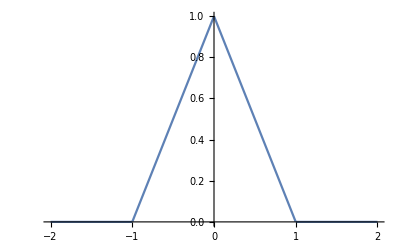

```mathematica
Plot[HeavisideLambda[x], {x,-2,2}]
```

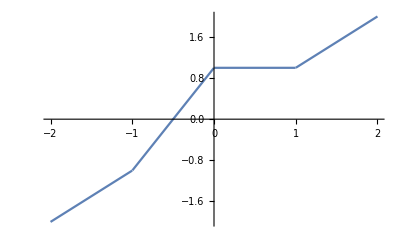

```mathematica
Plot[x+HeavisideLambda[x], {x,-2,2}]
```

```mathematica
Plot3D[HeavisideLambda[x,y],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
Histogram3D@Partition[Differences@Out[33],2,1,ColorData["AtlanticColors"]]
```

Histogram3D[Partition[{0.350729,0.255551,-0.315916,-0.0402494,-0.138017,0.47945,-0.392598,-0.63376,0.30812,0.423599,-0.834694,-0.177145,-0.300439,0.285115,-0.387074,-0.0400715,-0.00834244,-0.112464,0.505991,0.418309,-0.158311,-0.109622,0.0362748,-0.123361,-0.150968,0.0809177,0.00732875,0.400491,0.207818,0.680478,-0.200061,0.0150941,0.548077,-0.0750615,-0.0411011,0.26063,0.422231,-0.00757164,-0.214844,-0.104554,0.117624,-0.401325,-0.107891,0.274645,0.244916,0.364681,-0.15715,0.0216477,0.682723,0.241787,0.320591,-0.0528368,0.00454378,0.0998182,0.0338591,0.636971,-0.349349,-0.462477,-0.0423957,-0.360494,-0.258863,0.34602,0.770427,-0.349495,-0.815892,-0.258747,-0.141647,-0.148601,0.143858,0.0217362,0.146949,-0.450347,-0.270289,-0.729234,-0.330241,0.385353,-0.133739,0.25376,-0.191362,-0.610463,0.252602,0.322976,0.103679,0.212126,-0.15628,-0.0360242,0.287923,-0.213808,-0.296154,0.164693,0.0844437,-0.0858362,0.109503,0.160372,-0.327012,-0.151864,-0.526959,-0.490592,0.46419,-0.217757},2,1,ColorDataFunction[…]]]

```mathematica
Histogram3D[Partition[Differences@Out[33],2,1],ColorData["AtlanticColors"]]
```

-Graphics3D-

```mathematica
{
{1,1,-1,-1,-1,1,-1,-1,1,1,-1,-1,-1,1,-1,-1,-1,-1,1,1,-1,-1,1,-1,-1,1,1,1,1,1,-1,1,1,-1,-1,1,1,-1,-1,-1,1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,1,1,-1,-1,-1,-1,-1,1,1,-1,-1,-1,-1,-1,1,1,1,-1,-1,-1,-1,1,-1,1,-1,-1,1,1,1,1,-1,-1,1,-1,-1,1,1,-1,1,1,-1,-1,-1,-1,1,-1}
,
{buy,sell,hold,hold,buy,sell,hold,buy,hold,sell,hold,hold,buy,sell,-1,-1,-1,-1,1,1,-1,-1,1,-1,-1,1,1,1,1,1,-1,1,1,-1,-1,1,1,-1,-1,-1,1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,1,1,-1,-1,-1,-1,-1,1,1,-1,-1,-1,-1,-1,1,1,1,-1,-1,-1,-1,1,-1,1,-1,-1,1,1,1,1,-1,-1,1,-1,-1,1,1,-1,1,1,-1,-1,-1,-1,1,-1}
}
```

```mathematica
ListPlot[Out[33]]
```

-Graphics-

```mathematica
ListLinePlot[Out[33]]
```

-Graphics-